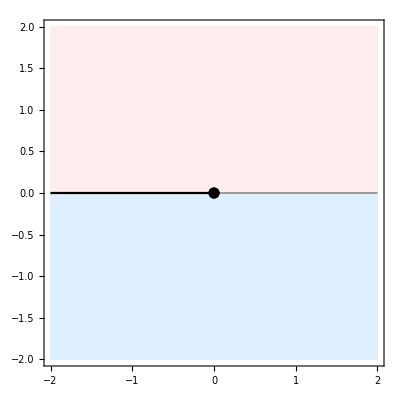

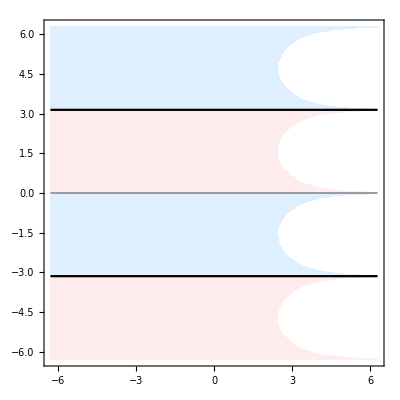

```mathematica
diag=1+I;
size=PointSize[0.02];
proc[f_,a_,b_]:=Module[{cp1,cp2},
cp1=ComplexContourPlot[
Im[f],{z,a-b*diag,a+b*diag},
Contours->{0},ContourShading->{LightBlue,LightPink}];
cp2=ComplexContourPlot[
Arg[-f]==0,{z,a-b*diag,a+b*diag},ContourStyle->Black];
Show[cp1,cp2]];
lp=ComplexListPlot[{0},PlotStyle->{Black,size}];
pz=Show[proc[z,0,2],lp]
pw=proc[Exp[z],0,2Pi]
```